# Fitting the binding curve

## Reading the data

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[], "2023.02.21.13.19.23"}]];
```

```mathematica
distances=BinaryReadList["distances.dat","Real32"];
angles=BinaryReadList["angles.dat","Real32"];
bindingEnergies=ArrayReshape[BinaryReadList["binding_energies.dat","Real32"],{Length[angles], Length[distances]}];
```

```mathematica
startingDistance={1, 2,3,5,};
```

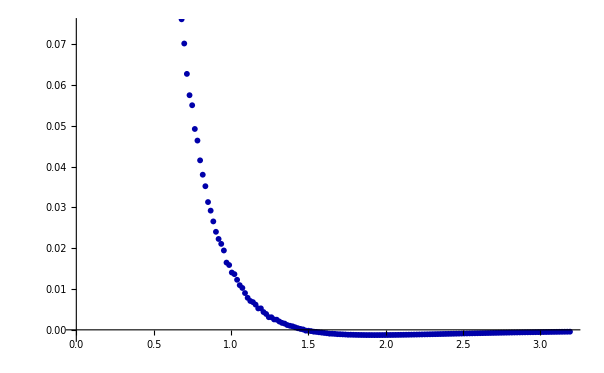

```mathematica
angleIDX=14;
startingDistance=18;
scatter=Table[{distances[[i]],bindingEnergies[[angleIDX,i]]},{i,startingDistance,Length[distances]-startingDistance}];
ListPlot[scatter,PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]]
```

```mathematica
13π/(2 19)//N
```

1.07476

```mathematica
π/2//N
```

1.5708

## Morse potential

```mathematica
angleIDX=14;
startingDistance=18;
scatter=Table[{distances[[i]],bindingEnergies[[angleIDX,i]]},{i,startingDistance,Length[distances]-startingDistance}];
```

```mathematica
nlm=Normal[NonlinearModelFit[scatter,De(Exp[-2a(r-re)]-2Exp[-a(r-re)]),{De,a,re},r]]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-39.5349 (ⅇ^(-11.5002 (0.527145+r))-2 ⅇ^(-5.75012 (0.527145+r)))

```mathematica
nlm=Normal[NonlinearModelFit[scatter,De(Exp[-a r]),{De,a},r]]
```

1.76114 ⅇ^(-3.36563 r)

```mathematica
nlm=Normal[NonlinearModelFit[scatter,4ϵ((σ/r)^12-(σ/r)^6),{ϵ,σ},r]]
```

1.50477 ((2.08395×10^-7)/r^12-0.000456503/r^6)

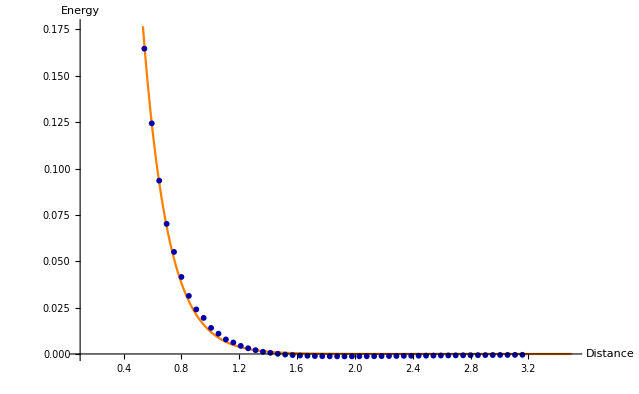

```mathematica
Clear[f]
f[r_]:=-39.53491142497741 (ⅇ^(-11.50023858598874 (0.5271449727957873+r))-2 ⅇ^(-5.75011929299437 (0.5271449727957873+r)))
Show[Plot[f[x],{x,0.1,3.5},PlotStyle->{Orange},AxesLabel ->{Distance,Energy}],ListPlot[scatter[[;; ;; 3]],PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]]]
```

```mathematica
FortranForm[0.46162512831719266 (ⅇ^(-5.473740049665798 (-0.5382686719819294+r))-2 ⅇ^(-2.736870024832899 (-0.5382686719819294+r)))]
```

0.46162512831719266*(E**(-5.473740049665798*(-0.5382686719819294 + r)) - 
     -    2/E**(2.736870024832899*(-0.5382686719819294 + r)))